```mathematica
x={84,85,87,79,106,112,67,98,78,87,86,116}
```

{84,85,87,79,106,112,67,98,78,87,86,116}

```mathematica
y={138,148,141,154,163,195,139,163,152,162,151,173}
```

{138,148,141,154,163,195,139,163,152,162,151,173}

```mathematica
y//Length
```

12

```mathematica
data=Table[{x[[k]],y[[k]]},{k,1,12}]
```

{{84,138},{85,148},{87,141},{79,154},{106,163},{112,195},{67,139},{98,163},{78,152},{87,162},{86,151},{116,173}}

```mathematica
solution=LinearModelFit[data,z,z]
```

FittedModel[75.5575+0.896138 z]

```mathematica
solution["BestFit"]
```

75.5575+0.896138 z

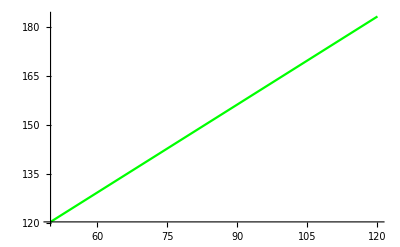

```mathematica
p1=Plot[75.55754673802096+0.8961377319297221 z,{z,50,120}, PlotStyle->Green]
```

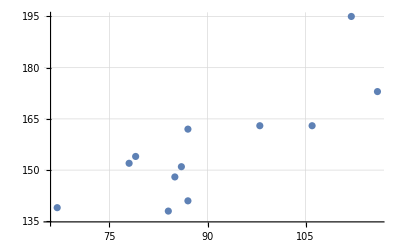

```mathematica
lp1=ListPlot[data,GridLines->Automatic]
```

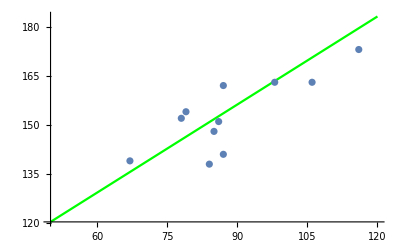

```mathematica
Show[p1,lp1]
```

```mathematica
LETS CHECK the other way:
```

```mathematica
corr = Correlation[x,y]
```

25453/(7 √20080921)

```mathematica
N[corr]
```

0.811426

```mathematica
slope = corr*StandardDeviation[y]/StandardDeviation[x]
```

25453/28403

```mathematica
N[slope]
```

0.896138

```mathematica
"above was our b_1"
```

```mathematica
intercept=Mean[y]-slope*Mean[x]
```

2146061/28403

```mathematica
N[intercept]
```

75.5575

```mathematica
"above was our b_0"
```